```mathematica
Clear["`*"];
```

## ballistic coefficient

## state variables

```mathematica
x={z, vz, β}
```

{z,vz,β}

## differential equations

```mathematica
MatrixForm[eqns={vz,0.0034 Exp[-z/22000] vz^2 / 2 / β-g,0}]
```

(vz
-g+(0.0017 ⅇ^(-z/22000) vz^2)/β
0)

## reference trajectory

equations

```mathematica
MatrixForm[eqns]
```

(vz
-g+(0.0017 ⅇ^(-z/22000) vz^2)/β
0)

steady state vz

```mathematica
MatrixForm[Solve[0.0034 Exp[-z/22000] vz^2 / 2 / β==g,vz]]
```

(vz→-24.2536 ⅇ^(0.0000227273 z) √g √β
vz→24.2536 ⅇ^(0.0000227273 z) √g √β)

```mathematica
svz=Solve[0.0034 Exp[-vz t/22000] vz^2 / 2 / β0==g,vz]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{vz→-(44000. ProductLog[-0.000551217 √(g t^2 β0)])/t},{vz→-(44000. ProductLog[0.000551217 √(g t^2 β0)])/t}}

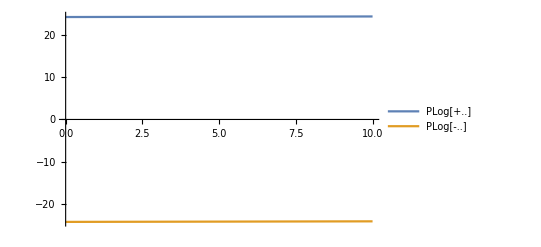

```mathematica
Plot[{(vz/.svz[[1]])/.{β0->1,g->1},{(vz/.svz[[2]])/.{β0->1,g->1}}},{t,0,10}, PlotLegends->{"PLog[+..]","PLog[-..]"}]
```

trajectory

```mathematica
MatrixForm[Transpose[ref={{vzn->vz/.svz[[2]],z->vzn t,vz->vzn,β->β0}}]]
```

(vzn→-(44000. ProductLog[0.000551217 √(g t^2)])/t
z→t vzn
vz→vzn
β→1)

test solution

```mathematica
MatrixForm[eqns]
```

(vz
-g+(0.0017 ⅇ^(-z/22000) vz^2)/β
0)

```mathematica
MatrixForm[(eqns//.ref[[1]])]
```

(-(44000. ProductLog[0.000551217 √(g t^2)])/t
-g+(3.2912×10^6 ⅇ^(2. ProductLog[0.000551217 √(g t^2)]) ProductLog[0.000551217 √(g t^2)]^2)/t^2
0)

2nd eq. should be zero.

```mathematica
eq2=(eqns//.ref[[1]]/.svz[[2]])[[2]]
```

-g+(3.2912×10^6 ⅇ^(2. ProductLog[0.000551217 √(g t^2)]) ProductLog[0.000551217 √(g t^2)]^2)/t^2

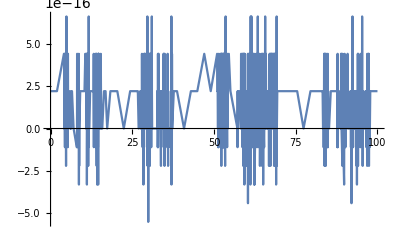

```mathematica
Plot[eq2/.{g->1,β0->1},{t,0,100}]
```

practically zero.

## Linearization

A matrix

```mathematica
MatrixForm[dfdx=D[eqns,{x}]]
```

(0 | 1 | 0
-(7.72727×10^-8 ⅇ^(-z/22000) vz^2)/β | (0.0034 ⅇ^(-z/22000) vz)/β | -(0.0017 ⅇ^(-z/22000) vz^2)/β^2
0 | 0 | 0)

reference trajectory substitution

```mathematica
MatrixForm[A=dfdx//.ref[[1]]]
```

(0 | 1 | 0
-(149.6 ⅇ^(2. ProductLog[0.000551217 √(g t^2)]) ProductLog[0.000551217 √(g t^2)]^2)/t^2 | -(149.6 ⅇ^(2. ProductLog[0.000551217 √(g t^2)]) ProductLog[0.000551217 √(g t^2)])/t | -(3.2912×10^6 ⅇ^(2. ProductLog[0.000551217 √(g t^2)]) ProductLog[0.000551217 √(g t^2)]^2)/t^2
0 | 0 | 0)

# final form

```mathematica
MatrixForm[MatrixForm[A.x]]
```

(vz
-(149.6 ⅇ^(2. ProductLog[0.000551217 √(g t^2)]) vz ProductLog[0.000551217 √(g t^2)])/t-(149.6 ⅇ^(2. ProductLog[0.000551217 √(g t^2)]) z ProductLog[0.000551217 √(g t^2)]^2)/t^2-(3.2912×10^6 ⅇ^(2. ProductLog[0.000551217 √(g t^2)]) β ProductLog[0.000551217 √(g t^2)]^2)/t^2
0)

observability

```mathematica
ssm=StateSpaceModel[{A,{{0},{0},{0}},{{1,0,0}}}]
```

0100-(149.6 ⅇ^(2. ProductLog[0.000551217 √(g t^2)]) ProductLog[0.000551217 √(g t^2)]^2)/t^2-(149.6 ⅇ^(2. ProductLog[0.000551217 √(g t^2)]) ProductLog[0.000551217 √(g t^2)])/t-(3.2912×10^6 ⅇ^(2. ProductLog[0.000551217 √(g t^2)]) ProductLog[0.000551217 √(g t^2)]^2)/t^2000001000StateSpaceModelFalseFalseFalseFalse$CellContext`stname1$CellContext`stname2$CellContext`stname3Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic1131FalseFalseFalseAutomaticNoneAutomatic

```mathematica
MatrixForm[qs=ObservabilityMatrix[ssm]]
```

(1 | 0 | 0
0. | 1. | 0.
0.-(149.6 ⅇ^(2. ProductLog[0.000551217 √(g t^2)]) ProductLog[0.000551217 √(g t^2)]^2)/t^2 | 0.-(149.6 ⅇ^(2. ProductLog[0.000551217 √(g t^2)]) ProductLog[0.000551217 √(g t^2)])/t | 0.-(3.2912×10^6 ⅇ^(2. ProductLog[0.000551217 √(g t^2)]) ProductLog[0.000551217 √(g t^2)]^2)/t^2)

```mathematica
MatrixRank[qs]==Length[A]
```

True

luenberger gains

```mathematica
MatrixForm[Eigenvalues[A]]
```

(0.
(0.5 (-149.6 ⅇ^(2. ProductLog[0.000551217 √(g t^2)]) t ProductLog[0.000551217 √(g t^2)]-√(-598.4 ⅇ^(2. ProductLog[0.000551217 √(g t^2)]) t^2 ProductLog[0.000551217 √(g t^2)]^2+22380.2 ⅇ^(4. ProductLog[0.000551217 √(g t^2)]) t^2 ProductLog[0.000551217 √(g t^2)]^2)))/t^2
(0.5 (-149.6 ⅇ^(2. ProductLog[0.000551217 √(g t^2)]) t ProductLog[0.000551217 √(g t^2)]+√(-598.4 ⅇ^(2. ProductLog[0.000551217 √(g t^2)]) t^2 ProductLog[0.000551217 √(g t^2)]^2+22380.2 ⅇ^(4. ProductLog[0.000551217 √(g t^2)]) t^2 ProductLog[0.000551217 √(g t^2)]^2)))/t^2)